```mathematica
ClearAll["Global`*"];
(*Sanki zsuwają się ze szczytu toru o długości L=30 m, pochylonego
pod kątem α do poziomu, a następnie wjeżdżają na tor poziomy. W
trakcie ruchu sanek na całej trasie działa na nie siła tarcia. Współczynnik tarcia wynosi k. Sporządzić:
1) Wykres obrazujący zależność prędkości,jaką będą miały sanki u podnóża pochyłego toru,od kąta α dla α zmieniającego się w zakresie od 15° do 25°.
2)Wykres obrazujący zależność drogi,jaką pokonają sanki na odcinku
poziomym od kąta α dla α zmieniającego się w zakresie od 15° do 25°.
Oba wykresy wykonać dla dwóch wartości współczynnika k: k=0.15 oraz k=0.20.*)
```

```mathematica
(*Wyprowadzenie wzorów na składową siły ciężkości równoległą do powierzchni toru "F"
(powodującą ruch sanek w dół) i na składową prostopadłą do powierzchni toru "FN"
(powodującą nacisk sanek na powierzchnię toru).Symbol "m" oznacza masę sanek,a "g" przyspieszenie ziemskie.*)
F=m×g×Sin[α Degree];
FN=m×g×Cos[α Degree];
```

```mathematica
T1=FN×k;
T2=m×g×k;
```

```mathematica
W1=F×L-T1×L;
```

```mathematica
Ek=(m×v^2)/2;
```

```mathematica
rown1=Solve[W1==Ek,v]
```

{{v→-√2 √(-g k L Cos[° α]+g L Sin[° α])},{v→√2 √(-g k L Cos[° α]+g L Sin[° α])}}

```mathematica
vd=v/. rown1[[2,1]]
```

√2 √(-g k L Cos[° α]+g L Sin[° α])

```mathematica
W2=T2×Lpoz;
```

```mathematica
rown2=Solve[W2==Ek,Lpoz]
```

{{Lpoz→v^2/(2 g k)}}

```mathematica
Lpoz=Lpoz/.rown2[[1]]/.v->vd
```

(-g k L Cos[° α]+g L Sin[° α])/(g k)

```mathematica
g=9.81 ;(* m/s^2 *)
```

```mathematica
L= 30; (* m *)
```

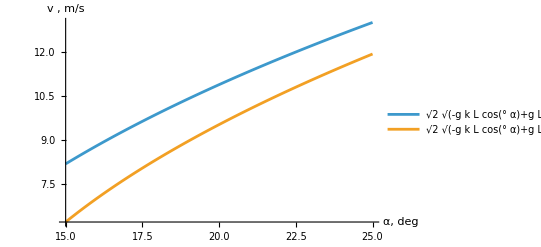

```mathematica
rys1=Plot[{vd/.k->0.15,vd/.k->0.20},{α,15,25},AxesLabel->{"α, deg","v , m/s "},PlotLegends->"Expressions"]
```

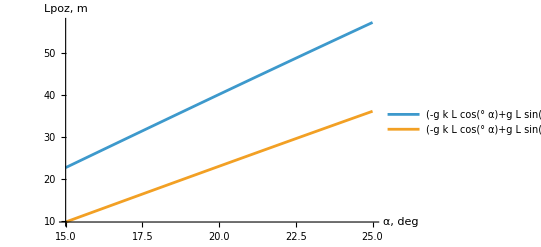

```mathematica
rys1=Plot[{Lpoz/.k->0.15,Lpoz/.k->0.20},{α,15,25},AxesLabel->{"α, deg","Lpoz, m "},PlotLegends->"Expressions"]
```